# Masterthesis Plots

```mathematica
(*Initialization Cell*)
$PlotTheme="Monochrome";
fontFamily=FontFamily->"Latin Modern Math"
commonPlotOptions={FrameStyle->Directive[Evaluate@fontFamily, FontSize->14]
,LabelStyle->Directive[Evaluate@fontFamily, FontSize->16,Black]
,Frame->True
,GridLines->Automatic
,ImageSize->Large
};
nonGridPlotOptions={FrameStyle->Directive[Evaluate@fontFamily, FontSize->14]
,LabelStyle->Directive[Evaluate@fontFamily, FontSize->16,Black]
,Frame->True
};
smallPlotOptions={Frame->True
,FrameStyle->Directive[Evaluate@fontFamily, FontSize->14]
,LabelStyle->Directive[Evaluate@fontFamily, FontSize->16,Black]
,GridLines->Automatic};
smallListPlotOptions={Evaluate@smallPlotOptions,PlotMarkers->{Automatic,Tiny}};
plot3DOptions={LabelStyle->Directive[Evaluate@fontFamily, FontSize->12,Black]};
listPlotOptions={Evaluate@commonPlotOptions,PlotMarkers->{Automatic,1}};
dB[r_]:=20Log10@r;
fromDb[d_]:=10^(d/20)//N;
```

FontFamily→Latin Modern Math

Basic Waveforms

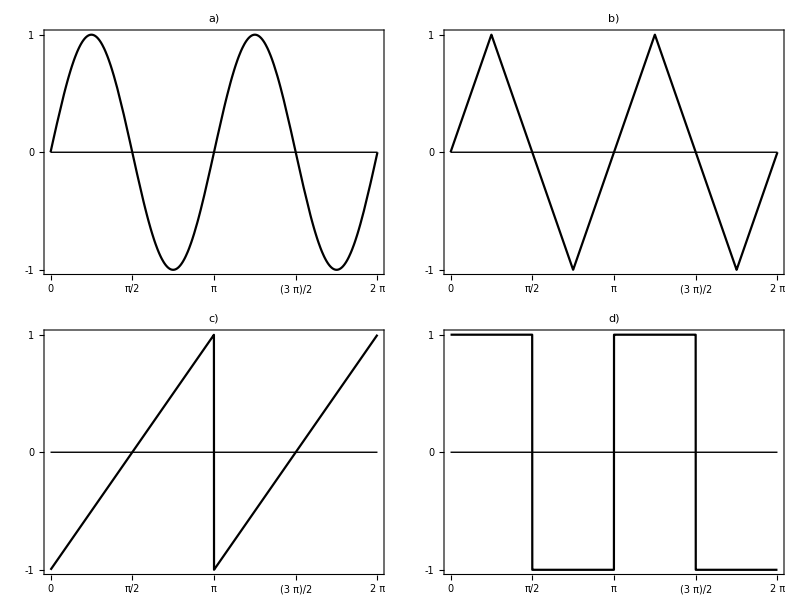

```mathematica
waveforms:={Sin[2Pi #]&,TriangleWave[#]&,2 SawtoothWave[#]-1&,SquareWave[#]&};
wavePlots:=MapThread[Plot[#1@x,{x,0,2}
,Evaluate@nonGridPlotOptions
,AspectRatio->1/2
,Exclusions->None
,PlotLabel->Style[#2]
,FrameTicks->{{{-1,0,1},None},{Table[{x,x Pi},{x,0,2,1/2}],None}}
,ImageSize->250
,Epilog->{Thin,Line[{{0,0},{2,0}}]}]&
,{waveforms,{"a)","b)","c)","d)"}}];
wavePlotsGrid=Grid[Partition[wavePlots,2]]
Export["/home/andreas/personal/edu/Uni-Leipzig/Masterarbeit/thesis/doc/imgs/basic-waveforms.pdf",wavePlotsGrid,"PDF"];
```

Discrete (sampled) sine

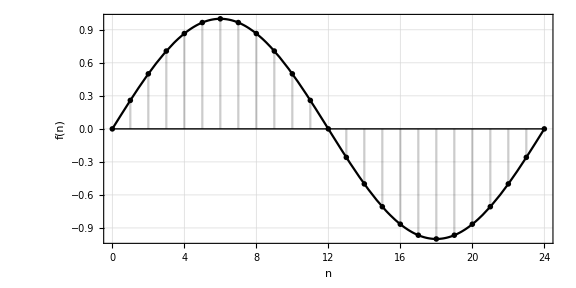

```mathematica
Module[{n,p1,p2},
n=24;
p1=DiscretePlot[Sin[2 Pi t/n],{t,0,n}
,PlotMarkers->{Automatic,Medium}
,Joined->False
,ExtentSize->None
,Epilog->{Thin,Line[{{0,0},{n,0}}]}
];
p2=Plot[Sin[t/n*2Pi],{t,0,n},Exclusions->None];
lookupPlot=Show[{p1,p2}
,FrameTicks->{{Automatic,Automatic}
,{Automatic,Table[{i,2Pi*i/n},{i,0,n,n/4}]}}
,FrameLabel->{"n","f(n)"}
,AspectRatio->1/2
,Evaluate@commonPlotOptions]]
Export["/home/andreas/personal/edu/Uni-Leipzig/Masterarbeit/thesis/doc/imgs/table-lookup.pdf",lookupPlot,"PDF"];
```

Sine wave spectrum

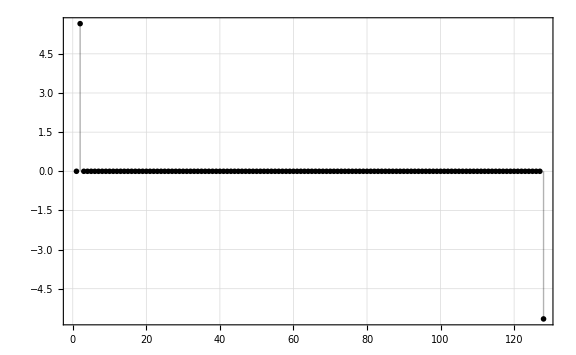

```mathematica
Module[{n},
n=128;ListPlot[Im@Fourier[Table[N@Sin[(t/n)*2Pi],{t,0,n-1}]]
,PlotRange->Full
,Filling->Axis
,Evaluate@commonPlotOptions]
]
```

Wavetable and spectrum

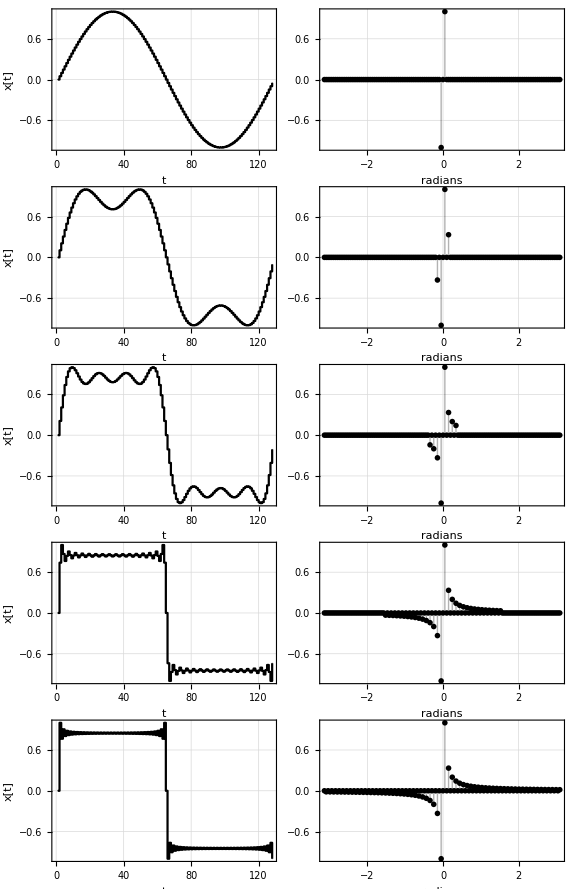

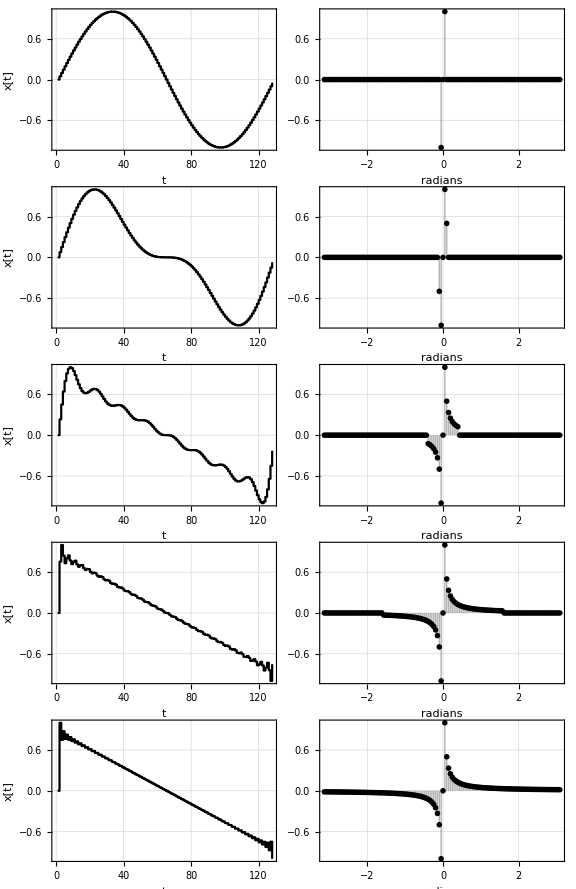

```mathematica
Module[{n,sr,dt,df,saw,sqr,rads},
n=128;
sr=64;
dt=1/sr;
df=sr/n;
saw[h_]:=RotateRight[Table[If[k==0||Abs[k]>h,0,I/k],{k,-n/2,n/2-1}],n/2];
sqr[h_]:=RotateRight[Table[If[EvenQ[k]||k==0||Abs[k]>h,0,I/k],{k,-n/2,n/2-1}],n/2];
rads=2Pi/n Range[-n/2,n/2-1];
plotsSaw =Table[{ListLinePlot[2Rescale[Re@InverseFourier[saw[k]]]-1
,PlotRange->{{0,n},{-1,1}}
,InterpolationOrder->0
,FrameLabel->{"t","x[t]"}
,Evaluate@listPlotOptions]
,ListPlot[MapThread[List,{rads,Im@RotateRight[saw[k],n/2]}]
,PlotRange->Full
, Filling->Axis
,FrameLabel->{"radians"}
,Evaluate@smallListPlotOptions]}
,{k,{1,2,8,n/4,n}}];
plotsSquare =Table[{ListLinePlot[2Rescale[Re@InverseFourier[sqr[k]]]-1
,PlotRange->Full
,InterpolationOrder->0
,FrameLabel->{"t","x[t]"}
,Evaluate@listPlotOptions]
,ListPlot[MapThread[List,{rads,Im@RotateRight[sqr[k],n/2]}]
,PlotRange->Full
, Filling->Axis
,FrameLabel->{"radians"}
,Evaluate@smallListPlotOptions]}
,{k,{1,4,8,n/4,n}}];
]
sqrPlot=GraphicsGrid[plotsSquare,Frame->False,ImageSize->Large,Spacings->0]
sawPlot=GraphicsGrid[plotsSaw,Frame->False,ImageSize->Large,Spacings->0]
Export["/home/andreas/personal/edu/Uni-Leipzig/Masterarbeit/thesis/doc/imgs/sqr-table.pdf",sqrPlot,"PDF"];
Export["/home/andreas/personal/edu/Uni-Leipzig/Masterarbeit/thesis/doc/imgs/saw-table.pdf",sawPlot,"PDF"];
```

Ration between input levels and db scale

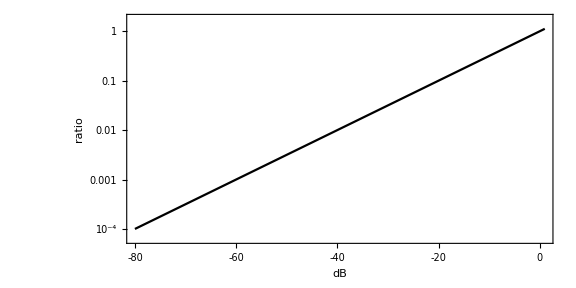

```mathematica
dB[r_]:=20Log10[r]//N;
dbPlot=LogPlot[10^(r/20),{r,1,-80}
,FrameTicks->{{{1,1/10,1/100,1/1000,1/10000}//N,None},{{0,-20,-40,-60,-80},None}}
,PlotRange->Full
,GridLines->Automatic
,FrameLabel->{"dB","ratio"}
,AspectRatio->1/2
,Evaluate@commonPlotOptions]
Export["/home/andreas/personal/edu/Uni-Leipzig/Masterarbeit/thesis/doc/imgs/db.pdf",dbPlot,"PDF"];
```

Table Interpolation

3.32982×10^6

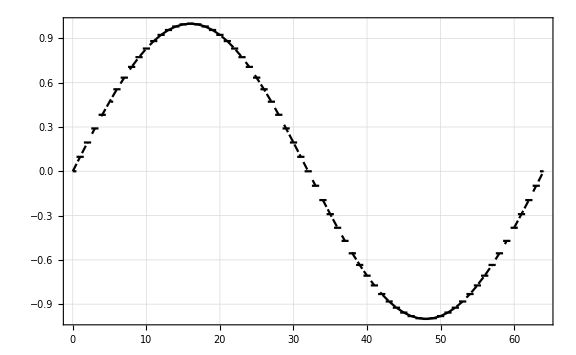
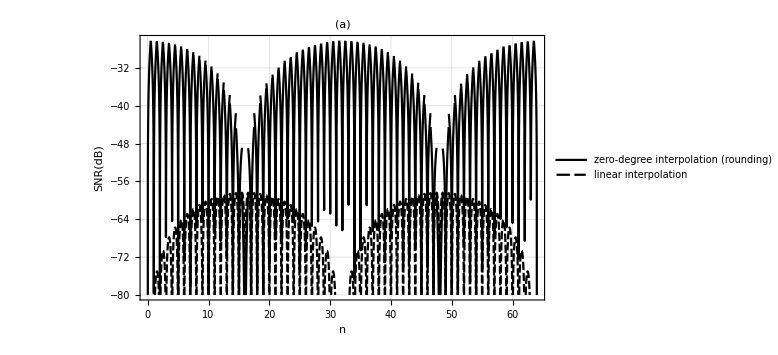

```mathematica
Module[{n,s,sRound,sInt},
n=64;
s[t_]:=Sin[t/n*2Pi];(* pure sine *)
sRound[t_]:=Sin[Round@t/n*2Pi]; (* sine zero-degree interpolation *)
sInt[t_]:=s[Floor@t]+(s[Floor@t+1]-s[Floor@t])(t-Floor@t);
sineSampledPlot=Plot[{sRound[x],sInt[x]},{x,0,n}
,PlotRange->{{0,n},{-1,1}}
,Evaluate@commonPlotOptions];(* sine with linear interpolation *)
interpolationErrorPlot=Plot[{dB@Abs[s@x-sRound@x],dB@Abs[s@x-sInt@x]},{x,0,n}
,PlotRange->{{0,n},{0,-80}}
,FrameLabel->{"n","SNR(dB)"}
,PlotLabel->"(a)"
,PlotLegends->Placed[{"zero-degree interpolation (rounding)","linear interpolation"},Below]
,Evaluate@commonPlotOptions];
t1:=Table[s@t-sRound@t//N,{t,0,n,1/n}];
t2:=Table[s@t-sInt@t//N,{t,0,n,1/n}]; 
dB@RootMeanSquare[t1]
dB@Max[t1]
dB@RootMeanSquare[t2]
dB@Max[t2]
]
{sineSampledPlot,interpolationErrorPlot}
Export["/home/andreas/personal/edu/Uni-Leipzig/Masterarbeit/thesis/doc/imgs/interpolation-error.pdf",interpolationErrorPlot,"PDF"];
```

Aliasing

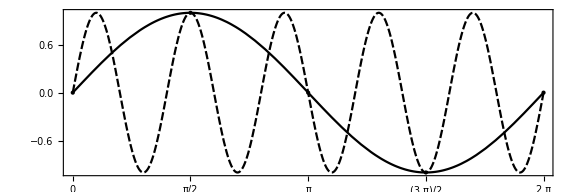

```mathematica
aliasPlot=Plot[{Sin[x],Sin[5x]},{x,0,2Pi}
,GridLines->{{Pi,2Pi},{-1,-.5,0,.5,1}}
,Epilog->{PointSize->Large,Point[Table[{n ,Sin[n]},{n,0,2Pi,Pi/2}]]}
,FrameTicks->{{Automatic,Automatic},{Table[n,{n,0,2Pi,Pi/2}],Automatic}}
,AspectRatio->1/3
,Evaluate@commonPlotOptions]
Export["/home/andreas/personal/edu/Uni-Leipzig/Masterarbeit/thesis/doc/imgs/aliasing.pdf",aliasPlot,"PDF"];
```

Foldover

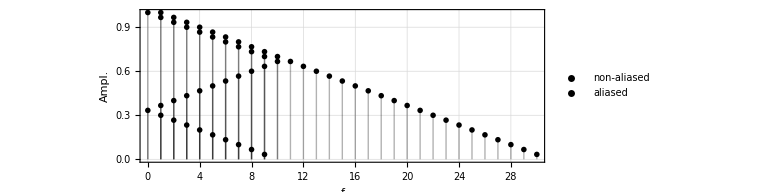

```mathematica
Module[{n,fa,max},
fa[f_,fs_]:=Abs@If[OddQ[Floor[f/fs]],(Floor[f/fs]+1) fs-f,Floor[f/fs] fs-f];
max=30;
foldoverPlot=ListPlot[{Table[1-n/max,{n,0,max-1}],Table[{fa[n,10],1-n/max},{n,0,max-1}]}
,PlotRange->All
,Filling->Axis
,AspectRatio->1/3
,PlotLegends->Placed[{"non-aliased","aliased"},Below]
,FrameLabel->{"f","Ampl."}
,FrameTicks->{Automatic,{Automatic,{{10,"f_Ny"}}}}
,Evaluate@commonPlotOptions
]
]
Export["/home/andreas/personal/edu/Uni-Leipzig/Masterarbeit/thesis/doc/imgs/foldover.pdf",foldoverPlot,"PDF"];
```

Fourier Series

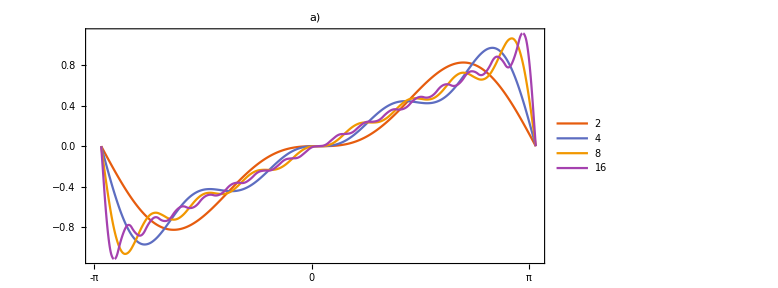

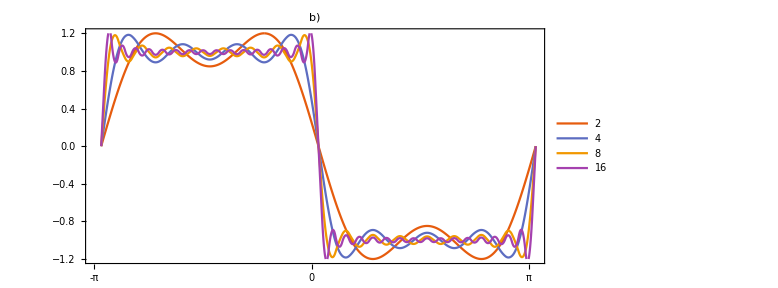

```mathematica
Module[{sr,harmonicsList,sawFouriers,sawWaves,sqrFouriers,sqrWaves,triFouriers,triWaves},
sr=64;
harmonicsList:={2,4,8,16};
sawFouriers:=Table[Table[If[n==0,0,(-1)^n Exp[-I 2Pi n t]/(n Pi)]
,{n,-harmonics,harmonics}]
,{harmonics,harmonicsList}];
sawWaves:=Im@Table[Total@(#/.t->t2//N),{t2,-.5,.5,1/sr}]&/@sawFouriers;
sqrFouriers:=Table[Table[If[n==0||EvenQ[n],0,2Exp[-I 2Pi n t]/(n Pi)]
,{n,-2harmonics,2harmonics}]
,{harmonics,harmonicsList}];
sqrWaves:=Im@Table[Total@(#/.t->t2//N),{t2,-.5,.5,1/sr}]&/@sqrFouriers;
triFouriers:=Table[Table[If[n==0||EvenQ[n],0,4Exp[-I 2Pi n t]/(n^2 Pi^2)]
,{n,-2harmonics,2harmonics}]
,{harmonics,harmonicsList}];
triWaves:=Re@Table[Total@(#/.t->t2//N),{t2,-.5+1/sr,.5-1/sr,1/sr}]&/@triFouriers;
sawPlot=ListLinePlot[sawWaves
,PlotLegends->Placed[harmonicsList,Above]
,AspectRatio->1/2
,InterpolationOrder->2
,PlotTheme->"Scientific"
,FrameTicks->{{{0,-Pi},{Round[sr/2],0},{sr,Pi}},Automatic}
,GridLines->None
,Evaluate@commonPlotOptions
,ImageSize->Small
,PlotLabel->"a)"];
sqrPlot=ListLinePlot[sqrWaves
,PlotLegends->Placed[harmonicsList,Above]
,AspectRatio->1/2
,InterpolationOrder->2
,PlotTheme->"Scientific"
,FrameTicks->{{{0,-Pi},{Round[sr/2],0},{sr,Pi}},Automatic}
,GridLines->None
,Evaluate@commonPlotOptions
,ImageSize->Small
,PlotLabel->"b)"];
]
sawPlot
sqrPlot
Export["/home/andreas/personal/edu/Uni-Leipzig/Masterarbeit/thesis/doc/imgs/fourier-series-saw.pdf",sawPlot,"PDF"];
Export["/home/andreas/personal/edu/Uni-Leipzig/Masterarbeit/thesis/doc/imgs/fourier-series-sqr.pdf",sqrPlot,"PDF"];
Export["/home/andreas/personal/edu/Uni-Leipzig/Masterarbeit/thesis/doc/imgs/fourier-series.pdf",{sawPlot,sqrPlot},"PDF"];
```

Theoretical SNR for single and double precision floating point values

```mathematica
(* machine epsilon, the negative exponent is the length of the significand (old mantissa) *)
N[dB[2^-24]]
N[dB[2^-53]]
N[dB[1/(2^(16-1))]]
```

-144.494

-319.092

-90.309

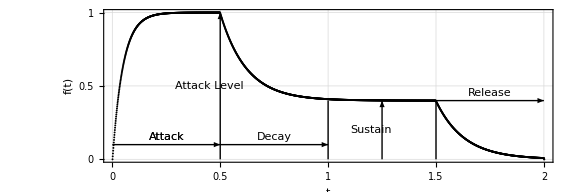

```mathematica
Module[{levels,fs,dur,durations,gains,aa,secTicks},
levels={1,0.4,0};
fs=1024;
dur[t_]:=Round[t fs];
durations={2,dur[.5],dur[1],dur[0.5]};
gains={0.02,0.008,0.0075};
aa = Table[0,Total@durations];
Do[aa[[n]]=levels[[1]]gains[[1]]+(1-gains[[1]])aa[[n-1]]
,{n,durations[[1]],durations[[2]]}];
Do[aa[[n]]=levels[[2]]gains[[2]]+(1-gains[[2]])aa[[n-1]]
,{n,durations[[2]],durations[[2]]+durations[[3]]}];
Do[aa[[n]]=levels[[3]]gains[[3]]+(1-gains[[3]])aa[[n-1]]
,{n,durations[[2]]+durations[[3]],durations[[2]]+durations[[3]]+durations[[4]]}];
secTicks:=Range[Length@aa]/fs;
adsr=ListPlot[Transpose@{secTicks,aa}
,AspectRatio->1/3
,FrameLabel->{"t","f(t)"}
,PlotMarkers->{Automatic,2}
,FrameTicks->{{{0,.5,1},None},{{0,.5,1,1.5,2},None}}
,Epilog->{{Arrowheads[{-Small,Small}]
,Evaluate@fontFamily
,FontSize->14
,Arrow[{{0.5,0},{.5,1}}],Text["Attack",{0.25,0.15}]
,Rotate[Text["Attack Level",{0.45,0.5}],90Degree]
,Arrow[{{0,.1},{.5,.1}}],Text["Attack",{0.25,0.15}]
,Arrow[{{.5,.1},{1,.1}}],Text["Decay",{0.75,0.15}]
,Arrow[{{1.25,0},{1.25,.4}}],Rotate[Text["Sustain",{1.2,0.2}],90 Degree]
,Arrow[{{1.5,.4},{2,.4}}],Text["Release",{1.75,.45}]}
,{Line[{{1.0,0},{1.0,0.4}}],Line[{{1.5,0},{1.5,0.4}}]}
}
,Evaluate@listPlotOptions]
]
Export["/home/andreas/personal/edu/Uni-Leipzig/Masterarbeit/thesis/doc/imgs/adsr.pdf",adsr,"PDF"];
```

Envelope transfer functions

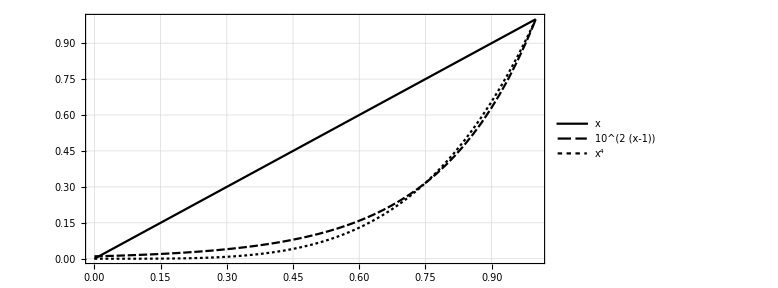

```mathematica
envelopeTransferFunctions=Plot[{x,10^(2(x-1)),x^4},{x,0,1}
,PlotLegends->"Expressions"
,AspectRatio->1/2
,Evaluate@commonPlotOptions]
Export["/home/andreas/personal/edu/Uni-Leipzig/Masterarbeit/thesis/doc/imgs/adsr-transfer-functions.pdf",envelopeTransferFunctions,"PDF"];
```

`ListSpectrumReal` returns the real spectrum of the given list

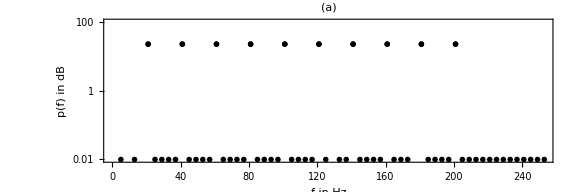

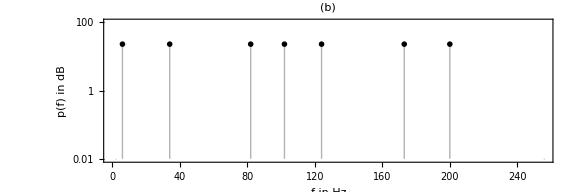

```mathematica
ListSpectrumReal[data_]:=Module[{scale,half,len},
len=Length@data;
scale=1/Sqrt[len/4];
half=If[EvenQ[len],Floor[len/2],Floor[len/2]+1];
scale Abs@Fourier[data[[All,2]],FourierParameters->{1,-1}][[;;half]]
];
Module[{sr,harmonics,inharmonics,hData,inhData},
sr=512;
harmonics=Table[20x,{x,1,10}];
inharmonics={33,123,81,5,101,172,199};
hData = Table[{t,Sum[Sin[2Pi fr t] ,{fr,harmonics}]//N},{t,0,1-1/sr,1/sr}];
inhData = Table[{t,Sum[Sin[2Pi fr t],{fr,inharmonics}]//N},{t,0,1-1/sr,1/sr}];
harmonicSpectrum=ListLogPlot[ListSpectrumReal@hData
,PlotRange->{Automatic,{0.01,100}}
,Filling->Axis
,AspectRatio->1/3
,FrameTicks->{{Automatic,None}, {Automatic,harmonics}}
,FrameLabel->{"f in Hz","p(f) in dB"}
,PlotLabel->"(a)"
,Evaluate@commonPlotOptions];
inharmonicSpectrum=ListLogPlot[ListSpectrumReal@inhData
,PlotRange->{Automatic,{0.01,100}}
,Filling->Axis,AspectRatio->1/3
,FrameTicks->{{Automatic,None}, {Automatic,inharmonics}}
,FrameLabel->{"f in Hz","p(f) in dB"},PlotLabel->"(b)"
,Evaluate@commonPlotOptions];
]
harmonicSpectrum
inharmonicSpectrum
Export["/home/andreas/personal/edu/Uni-Leipzig/Masterarbeit/thesis/doc/imgs/harmonic-spectrum.pdf",harmonicSpectrum,"PDF"];
Export["/home/andreas/personal/edu/Uni-Leipzig/Masterarbeit/thesis/doc/imgs/inharmonic-spectrum.pdf",inharmonicSpectrum,"PDF"];
```

Ring Modulation & FM Synthesis

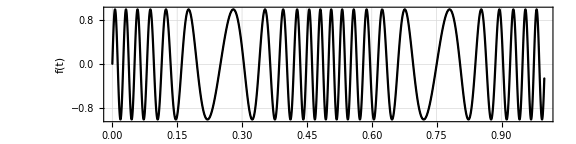

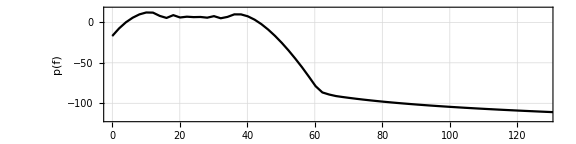

```mathematica
Module[{sr,cf,mf,ma,fmWave},
sr=1024;
cf=24;
mf=2;
ma=8;
fmWave:=Table[{t,Sin[2Pi cf t+ma Sin[2Pi mf t]]//N},{t,0,1-1/sr,1/sr}];
fmWavePlot=ListLinePlot[fmWave
,AspectRatio->1/4
,FrameLabel->{"t in s","f(t)"}
,InterpolationOrder->2
,Evaluate@listPlotOptions];
(* check the periodgram parameters *)
fmSpectrumPlot=Periodogram[fmWave[[All,2]],512,128,BlackmanWindow
,PlotRange->{{0,128},{-120,16}}
,SampleRate->sr
,AspectRatio->1/4
,Frame->True
,FrameLabel->{"f in Hz", "p(f)"}
,GridLines->Automatic
,Evaluate@listPlotOptions];
]
fmWavePlot
fmSpectrumPlot
Export["/home/andreas/personal/edu/Uni-Leipzig/Masterarbeit/thesis/doc/imgs/fm-wave.pdf",fmWavePlot,"PDF"];
Export["/home/andreas/personal/edu/Uni-Leipzig/Masterarbeit/thesis/doc/imgs/fm-spectrum.pdf",fmSpectrumPlot,"PDF"];
```

FM grid

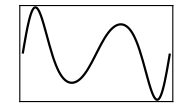
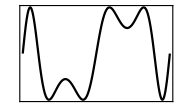
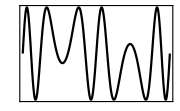
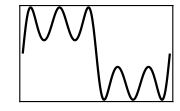
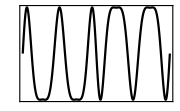
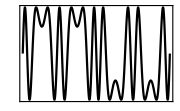
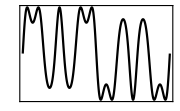
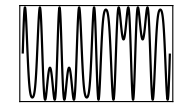
| a_m=1 | a_m=2 | a_m=4
f_m=1 | -Graphics- | -Graphics- | -Graphics-
f_m=2 | -Graphics- | -Graphics- | -Graphics-
f_m=4 | -Graphics- | -Graphics- | -Graphics-

| a_m=1 | a_m=2 | a_m=4
f_m=1 | -Graphics- | -Graphics- | -Graphics-
f_m=2 | -Graphics- | -Graphics- | -Graphics-
f_m=4 | -Graphics- | -Graphics- | -Graphics-

```mathematica
Module[{ams,fms,ts},
ams={1,2,4};
fms={1,2,4};
ts=Partition[Flatten@Table[{Subscript[a, m],Subscript[f, m],Sin[2Pi t+2 Subscript[a, m] Sin[2 Subscript[f, m] Pi t]]},{Subscript[f, m],fms},{Subscript[a, m],ams}],3];
fmPlots=Map[Plot[#[[3]],{t,0,1}
,PlotRange->Full
,Frame->True
(*,FrameTicks->{{{-1,0,1},None},{{0,.5,1},None}}*)
,FrameTicks->None
,ImageSize->Small
]&,ts];
fmGrid=TableForm[Partition[fmPlots,Length@ams]
,TableHeadings->{
Table[Text@Style[StringJoin@{"f_m=",ToString@Subscript[f, m]},FontFamily->"Latin Modern Math", FontSize->16],{Subscript[f, m],fms}]
,Table[Text@Style[StringJoin@{"a_m=",ToString@Subscript[a, m]},FontFamily->"Latin Modern Math", FontSize->16],{Subscript[a, m],ams}]
}
,TableAlignments->Center
,Directive[FontFamily->"Latin Modern Math", FontSize->16];
]
]
fmGrid
Export["/home/andreas/personal/edu/Uni-Leipzig/Masterarbeit/thesis/doc/imgs/fm-grid.pdf",fmGrid,"PDF"];
```

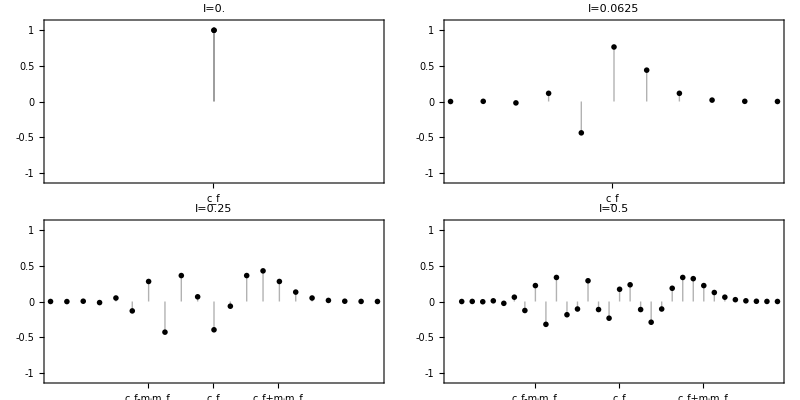

/home/andreas/personal/edu/Uni-Leipzig/Masterarbeit/thesis/doc/imgs/fm-bandwidth.pdf

```mathematica
Module[{sr,d,cf,mf,fm,modIndex},
sr=1024;d=1/sr;
modIndex={0,1,4,8};
cf=Floor@(sr/4);
mf=16;
fm[cf_,ma_,mf_,t_]:=Sin[2Pi cf t + ma Sin[2 Pi mf t]]//N;
fmBwPlots:=Table[
spectrum:=Fourier@Table[N@fm[cf,mod,mf,t],{t,0,1-d,d}];
magnitudeSpectrum:=Normalize@Im@spectrum[[;;Length[spectrum]/2]];
(* http://mathematica.stackexchange.com/questions/85278/is-there-a-built-in-equivalent-to-pythons-enumerate#comment231561_85302 *)
ListPlot[Select[MapIndexed[Append[#2,#1]&,magnitudeSpectrum],Abs@#[[2]]>0.0001&]
,PlotRange->{Automatic,{-1.1,1.1}}
,ImageSize->Large
,Filling->Axis
,AspectRatio->1/2
(*,GridLines->{{-cf/2,cf,3cf/2},{-.75,-.25,.25,.75}}*)
,GridLines->None
,PlotLabel->StringJoin["I=",ToString[N@(mod/mf)]]
,FrameTicks->{
{{-1,-.5,0,.5,1},None}
,If[mod>3
,{{{cf-mod mf, "c_f-m_im_f"},{cf,"c_f"},{cf+mod mf, "c_f+m_im_f"}},None}
,{{{cf,"c_f"}},None}
]
}
,Evaluate@smallPlotOptions
,PlotMarkers->{Automatic,Tiny}]
,{mod,modIndex}];
]
fmBwPlotGrid=GraphicsGrid[Partition[fmBwPlots,2],ImageSize->Full,Spacings->0]
Export["/home/andreas/personal/edu/Uni-Leipzig/Masterarbeit/thesis/doc/imgs/fm-bandwidth.pdf",fmBwPlotGrid,"PDF"]
```

Chowning FM page 5

```mathematica
besselPlot=Plot3D[BesselJ[i,t],{i,0,20},{t,0,20}
,PlotStyle->None
,PlotPoints->60
,PlotRange->{Automatic,Automatic,{-1,1}}
,ViewPoint->{Pi,.9Pi,Pi}
,BoundaryStyle->{Thick,Black}
,FaceGrids->{{{0,-1,0},{Table[n,{n,0,20}],Table[n/4,{n,-4,4}]}},{{-1,0,0},{Table[n,{n,0,20}],Table[n/4,{n,-4,4}]}}}
,FaceGridsStyle->LightGray
,Boxed->False
,ImageSize->Large
,AxesLabel->{"I","s_f"
,"s_A  "}
,Evaluate@plot3DOptions
]
Export["/home/andreas/personal/edu/Uni-Leipzig/Masterarbeit/thesis/doc/imgs/fm-bessel.pdf",besselPlot,"PDF"]
```

-Graphics3D-

/home/andreas/personal/edu/Uni-Leipzig/Masterarbeit/thesis/doc/imgs/fm-bessel.pdf

### Filter

Filter band example

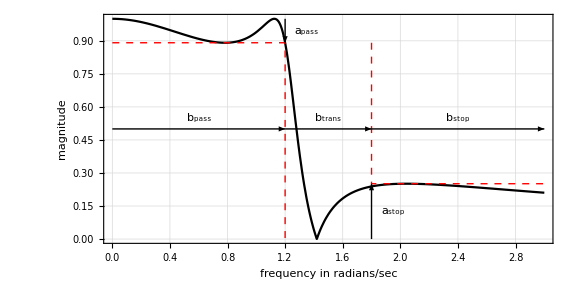

/home/andreas/personal/edu/Uni-Leipzig/Masterarbeit/thesis/doc/imgs/filter-bands.pdf

```mathematica
Module[{wpass,wstop,apass,astop,gpass,gstop,xmax,tf},
wpass=1.2;
wstop=1.8;
apass=1;
astop=12;
gpass=10^(-apass/20)//N;
gstop=10^(-astop/20)//N;
tf=EllipticFilterModel[{"Lowpass",{wpass,wstop},{apass,astop}}];
xmax=3;
bandPlot=Plot[Abs[tf[I*ω]],{ω,0,xmax}
,PlotRange->All
,Epilog->{
{Red,Dashed,Line[{{0,gpass},{wpass,gpass},{wpass,0}}],Line[{{wstop,gpass},{wstop,gstop},{xmax,gstop}}]}
,{Arrowheads[{-Small,Small}],Arrow[{{0,.5},{wpass,.5}}],Arrow[{{wpass,.5},{wstop,.5}}],Arrow[{{wstop,.5},{xmax,.5}}],
Arrow[{{wpass,1},{wpass,gpass}}],Arrow[{{wstop,0},{wstop,gstop}}]}
,Evaluate@fontFamily
,FontSize->14
,Text["b_pass",{wpass/2,.55}],Text["b_trans",{xmax/2,.55}]
,Text["b_stop",{wstop+(xmax-wstop)/2,.55}]
,Text["a_pass",{wpass+0.15,1-(1-gpass)/2}]
,Text["a_stop",{wstop+0.15,gstop/2}]
},Frame->{{True,False},{True,False}}
,AspectRatio->1/2
,FrameLabel->{"frequency in radians/sec","magnitude"}
,Evaluate@commonPlotOptions]
]
Export["/home/andreas/personal/edu/Uni-Leipzig/Masterarbeit/thesis/doc/imgs/filter-bands.pdf",bandPlot,"PDF"]
```

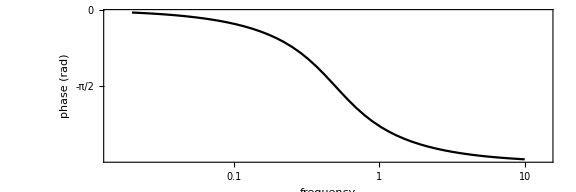

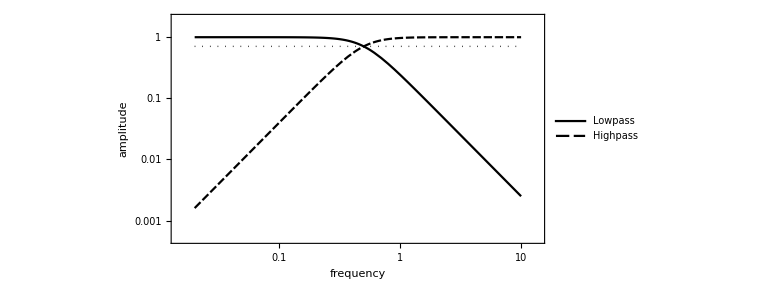
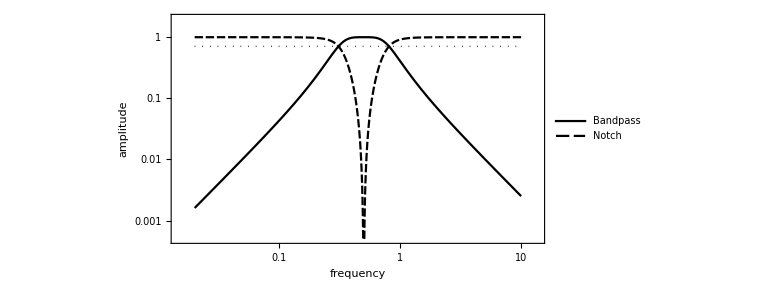

```mathematica
Module[{lp,hp,bp,bs,order=2,fc=.5,q=1,yTicks},
lp:=ButterworthFilterModel[{"Lowpass",order,fc}]//Chop//N;hp:=ButterworthFilterModel[{"Highpass",order,fc}]//Chop//N;
bp:=ButterworthFilterModel[{"Bandpass",order,{{fc,q}}}]//Chop//N;
bs:=ButterworthFilterModel[{"Bandstop",order,{{fc,q}}}]//Chop//N;
yTicks:=Table[{fromDb[n],n},{n,{-3,-12,-24,-36,-48,-60,-72}}];
lphpPlot=LogLogPlot[{Abs@lp[I f],Abs@hp[I f]},{f,0.02,10}
,FrameTicks->{{yTicks,None},{{{.02,0},{.1,.1},{.5,"f_c"},{1,1},{2,2},{5,5},{10,10}},None}}
,FrameLabel->{"frequency","amplitude"}
,PlotLegends->Placed[{"Lowpass","Highpass","Bandpass","Notch"},Below]
,PlotRange->{Automatic,{1/2000,2}}
,Epilog->{Dotted
,Thin
,Line[Log@{{0.02,fromDb[-3]},{10,fromDb[-3]}}]}
,AspectRatio->1/2
,ImageSize->Large
,Evaluate@nonGridPlotOptions];
bpbsPlot=LogLogPlot[{Abs@bp[I f],Abs@bs[I f]},{f,0.02,10}
,FrameTicks->{{yTicks,None},{{{.02,0},{.1,.1},{.5,"f_c"},{1,1},{2,2},{5,5},{10,10}},None}}
,FrameLabel->{"frequency","amplitude"}
,PlotLegends->Placed[{"Bandpass","Notch"},Below]
,PlotRange->{Automatic,{1/2000,2}}
,Epilog->{Dotted
,Thin
,Line[Log@{{0.02,fromDb[-3]},{10,fromDb[-3]}}]}
,AspectRatio->1/2
,ImageSize->Large
,Evaluate@nonGridPlotOptions];
phaseResponsePlot=LogLinearPlot[Arg@lp[I f],{f,0.02,10}
,FrameLabel->{"frequency","phase (rad)"}
,FrameTicks->{{Table[x Pi,{x,-1,0,1/2}],None},Automatic}
,PlotRange->All
,GridLines->Automatic
,AspectRatio->1/3
,ImageSize->Large
,Evaluate@nonGridPlotOptions]
]
filterClassification=Grid[{{lphpPlot},{bpbsPlot}},Frame->False]
Export["/home/andreas/personal/edu/Uni-Leipzig/Masterarbeit/thesis/doc/imgs/filter-classification.pdf",
filterClassification,"PDF"];
Export["/home/andreas/personal/edu/Uni-Leipzig/Masterarbeit/thesis/doc/imgs/filter-phase.pdf",phaseResponsePlot,"PDF"];
```

```mathematica
Filter Resonance
```

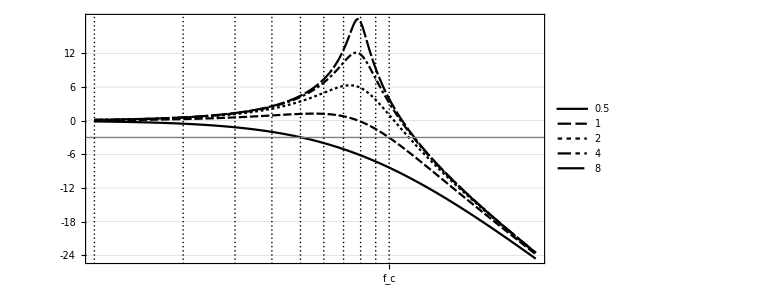

```mathematica
Module[{fc=Pi/4,
qs={0.5,1,2,4,8},lpfs,w},
lpfs=Table[BiquadraticFilterModel[{"Lowpass",{{fc,q}}}],{q,qs}];
resonancePlot=BodePlot[lpfs,{0.1,Pi//N}
,PlotLayout->"Magnitude"
,PlotLegends->Placed[qs,Below]
,AspectRatio->1/2
,FrameTicks->{{{12,6,0,-6,-12,-18,-24},None},{{{1,"f_c"}},None}}
,Epilog->{Gray,Line[{{Log@0.1,-3},{Log@10,-3}}]}
,Evaluate@commonPlotOptions]
]
Export["/home/andreas/personal/edu/Uni-Leipzig/Masterarbeit/thesis/doc/imgs/filter-resonance.pdf",resonancePlot,"PDF"];
```

Pole Zero Plot

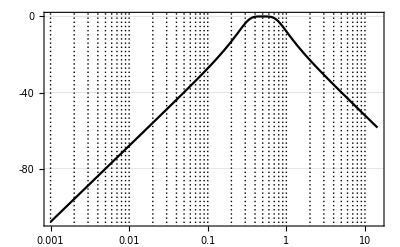

{-0.238801-0.680609 ⅈ,-0.238801+0.680609 ⅈ,-0.114752-0.327056 ⅈ,-0.114752+0.327056 ⅈ}

{0,0}

-Graphics-

```mathematica
poleZeroPlot=Module[{q=1,fc=0.5,tf,zeros,poles,zeroMarker,aa,bb,poleMarker},
(*tf=BiquadraticFilterModel[{"Bandpass",{{fc,q}}}];*)
tf=ButterworthFilterModel[{"Bandpass",2,{{fc,q}}}];
Print[BodePlot[tf,PlotLayout->"Magnitude",Evaluate@smallPlotOptions]];
poles=Flatten@TransferFunctionPoles[tf]//N//Chop;
zeros=Flatten@TransferFunctionZeros[tf]//N//Chop;
Print@poles;
Print@zeros;
zeroMarker=Graphics[{AbsolutePointSize[10],Point[{0,0}]}];
poleMarker=Graphics[{AbsoluteThickness[2],Line[{{1,1},{-1,-1}}],Line[{{-1,1},{1,-1}}]}];
ListPlot[{ReIm@poles,ReIm@zeros}
,PlotRange->1.2{{-1,1},{-1,1}}
,AspectRatio->1
,Epilog->{Gray,Circle[]}
,FrameLabel->{"Re","Im"}
,Evaluate@smallPlotOptions
,FrameTicksStyle->14
,PlotMarkers->{{poleMarker,0.04},{zeroMarker,1}}
]]
Export["/home/andreas/personal/edu/Uni-Leipzig/Masterarbeit/thesis/doc/imgs/filter-pole-zero.pdf",poleZeroPlot,"PDF"];
```

```mathematica
1
```

FIR Filter

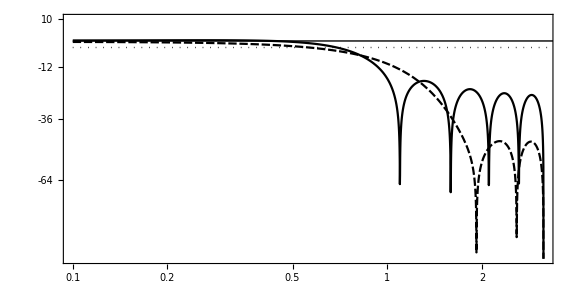

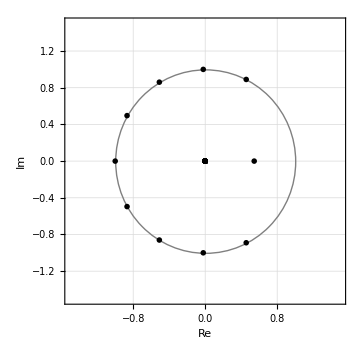

```mathematica
Module[{fc=Pi/4,order=12,lp,lpWindowed,win,H,tfm,zeros,zeroMarker},
lp=LeastSquaresFilterKernel[{"Lowpass",fc},order];
win=Array[HammingWindow,Length@lp,{-.5,.5}]//N;
lpWindowed =win lp;
H=TransferFunctionModel[ListZTransform[lp,z],z];
zeros=Flatten[ReIm@TransferFunctionZeros@H,2];
zeroMarker=Graphics[{AbsolutePointSize[9],Point[{0,0}]}];
firZeroPlot=ListPlot[zeros
,PlotRange->1.5{{-1,1},{-1,1}}
,Epilog->{Gray,Circle[]}
,FrameLabel->{"Re","Im"}
,Evaluate@smallPlotOptions
,FrameTicksStyle->14
,ImageSize->Medium
,PlotMarkers->{zeroMarker,1}
,AspectRatio->1];
LogLinearPlot[Evaluate[20Log10@Abs@ListFourierSequenceTransform[#,x]&/@{lp,lpWindowed}],{x,0.1,Pi}
,PlotRange->{{0.1,Pi},{-100,10}}
,AspectRatio->1/2
,FrameTicks->{{{10,-3,-12,-24,-36,-48,-64,-80},None},{{0,.01,.1,.5,1, 2},None}}
,Epilog->{{Dotted,Line[{{Log@0.1,-3},{Pi,-3}}]},{Line[{{Log@0.1,0},{Pi,0}}]}}
,Evaluate@commonPlotOptions]
]
firZeroPlot
Export["/home/andreas/personal/edu/Uni-Leipzig/Masterarbeit/thesis/doc/imgs/filter-zero-fir.pdf",firZeroPlot,"PDF"];
```